#### Geometric preliminaries

```mathematica
rrrot60=Table[MatrixPower[{{1/2,-√3/2},{√3/2,1/2}}//N,k],{k,0,5}]//Chop[#,10^-5]&
```

{{{1.,0},{0,1.}},{{0.5,-0.866025},{0.866025,0.5}},{{-0.5,-0.866025},{0.866025,-0.5}},{{-1.,0},{0,-1.}},{{-0.5,0.866025},{-0.866025,-0.5}},{{0.5,0.866025},{-0.866025,0.5}}}

```mathematica
rrrot90=Table[MatrixPower[{{0,-1},{1,0}}//N,k],{k,0,5}]//Chop[#,10^-5]&;
```

#### Splines, cleanpath

Flower with p fold symmetry, using the spline command:

```mathematica
cleanpath[path_,res_]:=Module[{ppath,i,rr},ppath={path⟦1⟧}; i=0;rr=res^2;
		While[i<Length[path],
			If[#.#&[ppath⟦-1⟧-path⟦i+1⟧]>rr,ppath=Append[ppath,path⟦i+1⟧]];i++];If[Length[ppath]>3,ppath]]
```

```mathematica
cleanpath[path_]:=cleanpath[path,.0005]
```

```mathematica
spline[x0_,x1_,v0_,v1_]:=
	a t^3+b t^2 + c t + d/.
		{a->-v1+v0-2x1+2x0,
			b->3x1-3x0-2v0+v1,
			c->v0,d->x0}
```

This is precisely the spline we know and love from Adobe Illustrator:

```mathematica
psBezier[x0_,x1_,c0_,c1_]:=spline[x0,x1,3(c0-x0),3(c1-x1)]
```

This is the ps command produced in eps2eps

```mathematica
rcurve2spline[x0_,y0_,dx1_,dy1_,dx2_,dy2_,dx3_,dy3_]:=
	psBezier[{x0,y0},{x0,y0}+{dx3,dy3},{x0,y0}+{dx1,dy1},{x0,y0}+{dx2,dy2}]
```

this handy command can take a list of rcurves and turn them into a list of points

```mathematica
producePath[{x0_,y0_},curveList_,steps_]:=
	Module[{ss,ii},
		ii=0;
		ss={};
		xi=x0;
		yi=y0;
		While[ii<Length[curveList],
			ii=ii+1;
			ss=Join[ss,
					(rcurve2spline@@Join[{xi,yi},curveList⟦ii⟧])//Table[#/.{t->tt},{tt,0,1,1/(steps+1)}]&];
			xi=xi+curveList⟦ii,5⟧;
			yi=yi+curveList⟦ii,6⟧;
			];
		ss
		]
```

```mathematica
producePath[{x0_,y0_},curveList_]:=producePath[{x0,y0},curveList,20]
```

Show[Graphics[Line[{10,20}+#&/@.2
				producePath[{267.62, 2.89},
{
{-453.34, 633.34, -273.34, 1146.68, 186.66, 940},
{460, -206.67, 1200, 540, 700, 260}
},10]],AspectRatio->Automatic]]

⁃Graphics⁃

```mathematica
ScalePath[pathPolygon[pp_],sscale_]:=pathPolygon[sscale pp];
ScalePath[pathSpline[pp_],sscale_]:=pathSpline[sscale pp];

ShiftPath[pathPolygon[pp_],sshift_]:=pathPolygon[(sshift+#)&/@ pp];
ShiftPath[pathSpline[pp_],sshift_]:=pathSpline[{sshift+pp⟦1⟧, pp⟦2⟧}];

TransformPath[pathPolygon[pp_],A_]:=pathPolygon[(A.#)&/@ pp];
TransformPath[pathSpline[pp_],A_]:=pathSpline[{A.pp⟦1⟧,
			Flatten[((#.Inverse[A])&/@(Table[{#⟦2i-1⟧,#⟦2i⟧},{i,1,Length[#]/2}])),1]&/@pp⟦2⟧}];


DrawPath[pathPolygon[pp_]]:=Line[pp];
DrawPath[pathSpline[pp_]]:=Line[producePath @@ pp];
DrawPath[pathPolygon[pp_],f_]:=f[pp];
DrawPath[pathSpline[pp_],f_]:=f[producePath @@ pp];
```

#### pathObjects in Perspective

vv is the shift off of {0,0} for the vanishing point; cc is the eye distance to the viewing plane, in units of 1; dd is the depth behind the viewing plane viewed in the field.

```mathematica
PutPathInPerspective[vv_,cc_,dd_][path_[pp_]]:=ShiftPath[ScalePath[ShiftPath[path[pp],-vv],
			cc/(dd+cc)],vv]
```

#### The ship

```mathematica
bubble=pathSpline[
	{{710,507},{{
-6.71, -1.19, -11.12, -0.04, -13.4, 3.42},{
-2.22, 3.42, -20, -3.52, -32.17, -26.56 },{
0, 0, 8.95, -12.61, 26.78, -13.7}}}];

dome=pathSpline[ {{290 ,-10}+{460.45,459.81},{{
0.08, -13.2, -22.7, -24, -50.79, -24.07},{
-28.11, -0.11, -50.94, 10.55, -50.98, 23.71},{

-0.15, 40.14, 22.52, 72.66, 50.64, 72.77},{
28.09, 0.04, 51.03, -32.3, 51.14, -72.43}}}];

ship= {{0,  229.04} ,  {460.46,  1.73}, { -95.96,  -98.07}, { 34.92,  -132.7},{  -399.42,  229.04}};
ss={460.45,230.766};sship=Table[ss=ship⟦i⟧+ss,{i,1,5}];


sship = pathPolygon[ sship];

groove=pathPolygon[{{460.45,459.806},{824.95,363.466}, {859.87,230.766}}];
theShip = {sship,dome, bubble,groove};
```

#### colors

```mathematica
ssFnc[Depth_]:=ArcTan[(Depth-1)/4]/Pi 2;
ssFnc[Depth_]:=Min[1.05(1-√(1/((Depth-1)^2/10+1))),1];


c0={255,255,200}/255. ;
c1={32,43,51}/255.;

coll={112,139,88};
col={{255,255,200},coll,{222,241,141},coll,{209,237,219}}/255.;
```

```mathematica
ColorFnctn[Depth_]:=GrayLevel[ssFnc[Depth]];
```

```mathematica
ColorFnctn[Depth_]:=RGBColor@@ (ssFnc[Depth] c1 +(1-ssFnc[Depth])c0) ;
```

```mathematica
ColorFnctn[Depth_,p_]:=RGBColor@@ (ssFnc[Depth] c1+(1-ssFnc[Depth])col[[p]]) ;
```

```mathematica
theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};
ttype={Polygon,Line,Polygon,Line,Polygon};
```

## Platycosms

### the ship

#### intially

```mathematica
theShip = {sship,dome, bubble};

theShip2=
	TransformPath[#,{{1/2,-√3/2},{√3/2,1/2}}]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.4}],.8],
						qq=.1;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.4,.4}],
					1.2]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));
```

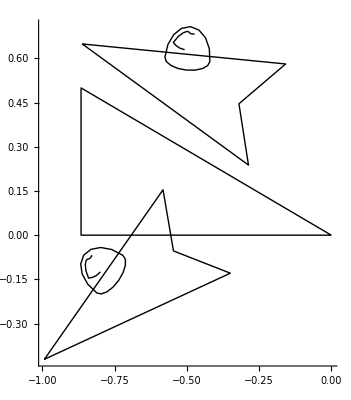

```mathematica
Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,
		{Line[{{0,0},{-√3/2,0},{-√3/2,1/2},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

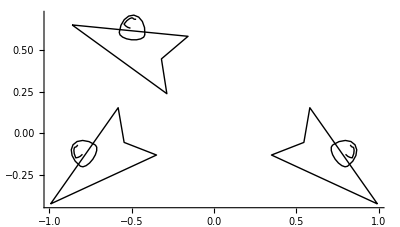

```mathematica
theShip3=TransformPath[#,{{-1,0},{0,1}}]&/@theShip2;

Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,DrawPath/@theShip3
	],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

#### hexacosm

```mathematica
(*theShip = {sship,dome, bubble};*)



theShip2=
	TransformPath[#,{{1/2,-√3/2},{√3/2,1/2}}]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.4}],.7],
						qq=-.9+Pi;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.4,.4}],
					1.2]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));
```

```mathematica
Show[Graphics[Join[(*DrawPath/@theShip2,*)DrawPath/@theShip,
		{Line[{{0,0},{-√3/2,0},{-√3/2,1/2},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

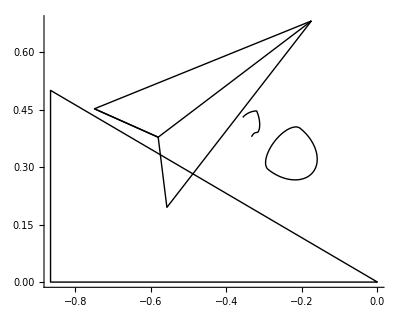

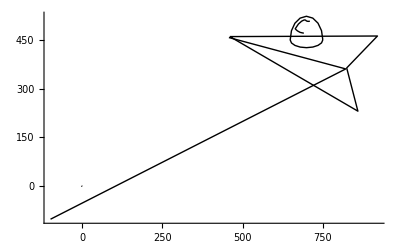

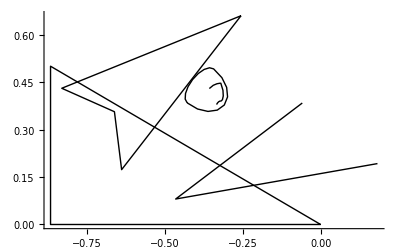

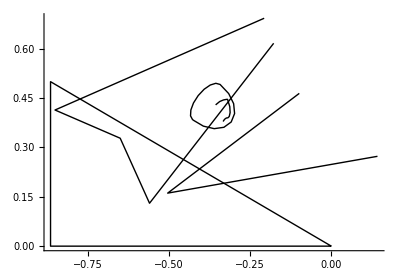

#### for the tetracosm

```mathematica
theShip = {sship,dome, bubble};

theShip2=
	TransformPath[#,rrrot90⟦2⟧]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.4}],1.2],
						qq=-1.15+Pi;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.4,.4}],
					1.2]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));
```

```mathematica
Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,
		{Line[{{0,0},{-1,0},{-1,1},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

⁃Graphics⁃

```mathematica
theShip = {sship,dome, bubble};

theShip2=
	TransformPath[#,rrrot90⟦2⟧]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.4}],.9],
						qq=-.5+Pi;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.23,.45}],
					1.7]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));

theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};
ttype={Polygon,Line,Polygon,Line,Polygon};


Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,
		{Line[{{0,0},{-1,0},{-1,1},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

⁃Graphics⁃

#### for the tricosm

```mathematica
theShip = {sship,dome, bubble};

theShip2=
	TransformPath[#,rrrot60⟦3⟧]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.3}],1.2],
						qq=-1.15+Pi;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.4,.4}],
					1.2]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));

		theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};

Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,
		{Line[{{0,0},{-1,0},{-1,1},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

⁃Graphics⁃

```mathematica
theShip = {sship,dome, bubble};

theShip2=
	TransformPath[#,rrrot60⟦3⟧]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.3}],1.2],
						qq=-1.4+Pi;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.55,.15}],
					1.2]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));

		theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};

Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,
		{Line[{{0,0},{-1,0},{-1,1},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

⁃Graphics⁃

#### for the dicosm

```mathematica
theShip = {sship,dome, bubble};

theShip2=
	TransformPath[#,rrrot90⟦3⟧]&/@ 
	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						ScalePath[
						ShiftPath[#,{.4,-.4}],1.5],
						qq=-.8+Pi;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						],{-.2,.4}],
					1.2]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));

		theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};

Show[Graphics[Join[DrawPath/@theShip2,DrawPath/@theShip,
		{Line[{{0,0},{-1,0},{-1,1},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

⁃Graphics⁃

### pictures

#### The torus

```mathematica
GridZ[ww_]:= (Join @@ Table[ {i,j} ,{i,-Ceiling[1.5 ww  +1/2],Ceiling[1.5 ww  +1/2]},
		{j,-Ceiling[1.5 ww+1/2],Ceiling[1.5 ww+1/2]}])
```

```mathematica
EyePoint = 5; vvP = {0,0};WWidth= 1;MaxDepth=7;		theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[4 (Depth-1),ppiece]},
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint, Depth][
				ShiftPath[theShipX⟦ppiece⟧,
					#]]&/@ ggg))],{Depth,MaxDepth,1,-1},{ppiece,1,5}]))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

⁃Graphics⁃

#### hexacosm & tricosm

```mathematica
v6={{√3,0},{0,3},{√3/2,3/2}}//N;
```

Enough vectors to cover a 2ww x 2 ww square.

```mathematica
Grid6[ww_]:=Join @@ (Join @@ Table[ i v6⟦1⟧+ j v6⟦2⟧ + k v6⟦3⟧ ,{i,-Ceiling[ww/√3 1.3+1/2],Ceiling[ww/√3 1.3+1/2]},
		{j,-Ceiling[ww/(√3+1)+1/2],Ceiling[ww/(√3+1)+1/2]},{k,0,1}])
```

```mathematica
EyePoint = 50; vvP = {0,0};WWidth= 1;MaxDepth=60;		

theShipX={theShip⟦1⟧,theShip⟦4⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};

col={{255,255,210},{245,243,200},coll, {222,241,141},coll*.97,{209,237,219}}/255.

ttype={Polygon,Polygon,Line,Polygon, Line,Polygon};
```

{{1.,1.,0.823529},{0.960784,0.952941,0.784314},{0.439216,0.545098,0.345098},{0.870588,0.945098,0.552941},{0.426039,0.528745,0.334745},{0.819608,0.929412,0.858824}}

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	Table[ggg = Grid6[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[Depth,ppiece]},
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,1.6 Depth][
				ShiftPath[
					TransformPath[theShipX⟦ppiece⟧,
						rrrot60⟦Mod[Depth,6]+1⟧],#]]&/@ ggg))],{Depth,MaxDepth,1,-1},{ppiece,1,6}]))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

-Graphics-

```mathematica
EyePoint = 50; vvP = {0,0};WWidth= 1;MaxDepth=30;		

Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	Table[ggg = Grid6[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[4 (Depth-1),ppiece]},
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint, 4  Depth][
				ShiftPath[
					TransformPath[theShipX⟦ppiece⟧,
						rrrot60⟦Mod[2*Depth,6]+1⟧],#]]&/@ ggg))],{Depth,MaxDepth,1,-1},{ppiece,1,5}]))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

⁃Graphics⁃

#### the tetracosm & dicosm

```mathematica
v4={{2,0},{0,2}}//N;
```

Enough vectors to cover a 2ww x 2 ww square.

```mathematica
Grid4[ww_]:=Join @@ (Table[ i v4⟦1⟧+ j v4⟦2⟧  ,{i,-Ceiling[ww/2 1.3+1/2],Ceiling[ww/2  1.3+1/2]},
		{j,-Ceiling[ww/2+1/2],Ceiling[ww/2+1/2]}])
```

```mathematica
EyePoint = 50; vvP = {0,0};WWidth= 1;MaxDepth=40;
```

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	Table[ggg = Grid4[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[2Depth,ppiece]},
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP, EyePoint,4 Depth][
				ShiftPath[
					TransformPath[theShipX⟦ppiece⟧,
						rrrot90⟦Mod[Depth,4]+1⟧],#]]&/@ ggg))],{Depth,MaxDepth,1,-1},{ppiece,1,5}]))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

-Graphics-

```mathematica
EyePoint = 50; vvP = {0,0};WWidth= 1;MaxDepth=20;
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	Table[ggg = Grid4[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[5 (Depth-1),ppiece]},
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,8 Depth][
				ShiftPath[
					TransformPath[theShipX⟦ppiece⟧,
						rrrot90⟦Mod[2 Depth,4]+1⟧],#]]&/@ ggg))],{Depth,MaxDepth,1,-1},{ppiece,1,5}]))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

⁃Graphics⁃

#### the amphicosms

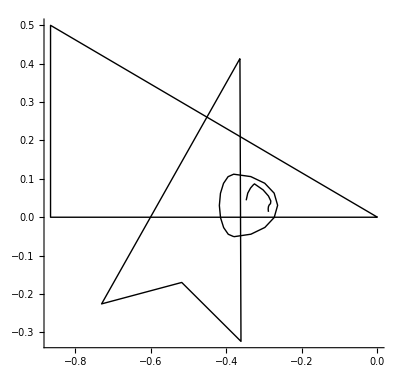

```mathematica
theShip = {sship,dome, bubble};


	(theShip=
				ScalePath[
				ShiftPath[
					TransformPath[
						#,
						qq=Pi/2;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						], {-.9,-.4}],
					1]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));

theShipX={theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};

Show[Graphics[Join[DrawPath/@theShip,
		{Line[{{0,0},{-√3/2,0},{-√3/2,1/2},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

```mathematica
ss=2;
GridZ[ww_]:= (Join @@ Table[ {ss i,ss j} ,{i,-Ceiling[1.5 ww /ss +1/2],Ceiling[1.5 ww /ss +1/2]},
		{j,-Ceiling[1.5 ww/ss +1/2],Ceiling[1.5 ww/ss +1/2]}])
```

```mathematica
ttype={Polygon,Line,Polygon,Line,Polygon};
```

```mathematica
EyePoint = 50; vvP = {0,0};WWidth= 1;MaxDepth=16;
```

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[
					TransformPath[ShiftPath[TransformPath[ShiftPath[
																				theShipX⟦ppiece⟧,{.5,0}],{{(-1)^flip,0},{0,1}}],{-.5,0}],
																	
																	
																	
																	
						rrrot90⟦Mod[Depth,2] 2+1⟧],#+{0,flip}]]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

-Graphics-

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[
					TransformPath[
																	
																	ShiftPath[
																	
																	TransformPath[
																			
																			ShiftPath[
																				theShipX⟦ppiece⟧,{.5,0}],{{(-1)^flip,0},{0,1}}],{-.5,0}],
																	
																	
																	
																	
						{{(-1)^Mod[Depth,2],0},{0,1}}],#+{0,flip}]]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

⁃Graphics⁃

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[
					TransformPath[
																	
																
																	TransformPath[
																			
																	
																				theShipX⟦ppiece⟧,{{(-1)^flip,0},{0,1}}],
																	
																	
																	
																	
						{{(-1)^Mod[Depth,2],0},{0,1}}],#+{0,flip}]]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

⁃Graphics⁃

```mathematica
MaxDepth=16;
```

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[
					TransformPath[
																	
																
																	TransformPath[
																			
																	
																				theShipX⟦ppiece⟧,{{(-1)^flip,0},{0,1}}],
																	
																	
																	
																	
						rrrot90⟦Mod[Depth+1,2] 2+1  ⟧],#+{0,flip}]]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

⁃Graphics⁃

#### New amphicosm pix

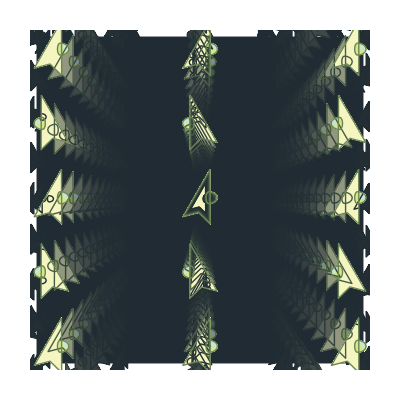

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[ShiftPath[
TransformPath[ShiftPath[

theShipX⟦ppiece⟧,{.5,0}],

{{(-1)^flip,0},{0,1}}],{0,flip}],#]

]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

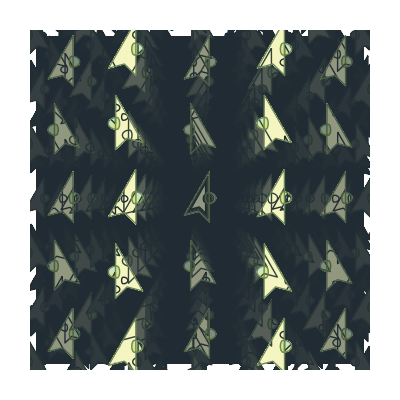

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[ShiftPath[ShiftPath[
TransformPath[ShiftPath[

theShipX⟦ppiece⟧,{.5,0}],

{{(-1)^flip,0},{0,1}}],{0,flip}],

{Mod[Depth,2],0}

],#]

]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

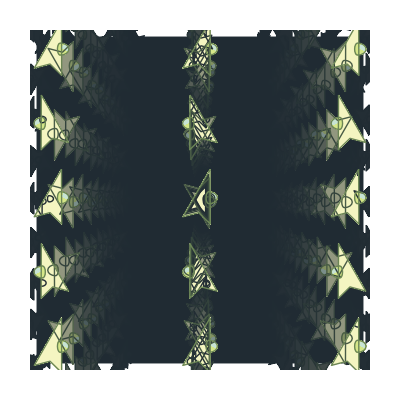

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[ShiftPath[
TransformPath[ShiftPath[

theShipX⟦ppiece⟧,{.5,0}],

{{(-1)^flip,0},{0,(-1)^(Depth+1)}}],{0,flip}],#]

]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

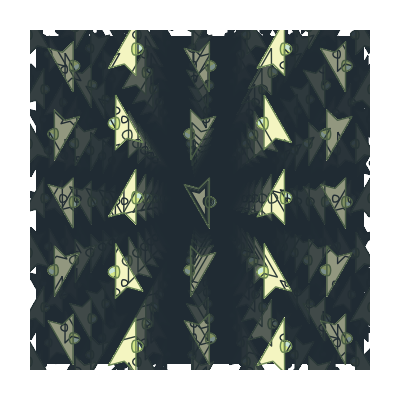

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ (Join @@	(Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
						Join[{ColorFnctn[6 (Depth-1),ppiece]},
									
				(DrawPath[#,ttype[[ppiece]]]&/@(	PutPathInPerspective[vvP,EyePoint,5 Depth][
				ShiftPath[ShiftPath[ShiftPath[
TransformPath[ShiftPath[

theShipX⟦ppiece⟧,{.5,0}],

{{(-1)^flip,0},{0,(-1)^(Depth+1)}}],{0,flip}],

{Mod[Depth,2],0}

],#]

]&/@ (ggg)))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{ppiece,1,5}])))
			
			
		
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

#### didicosm

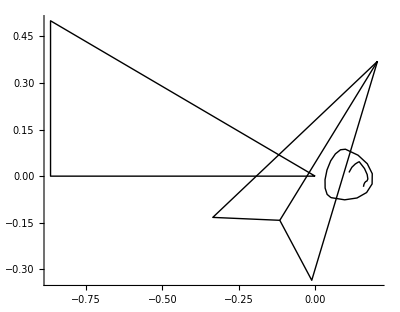

```mathematica
groove=pathPolygon[{{460.45,459.806},{824.95,363.466}}];
theShip = {sship,dome, bubble,groove};


	(theShip=TransformPath[
				ScalePath[
				ShiftPath[
					TransformPath[
						#,
						qq=Pi/2;
						{{Cos[qq],Sin[qq]},{-Sin[qq],Cos[qq]}}
						], {-.45,-.4}],
					1],
			ppX=.3;
				{{Cos[ppX],Sin[ppX]},{-Sin[ppX],Cos[ppX]}}]
							
							&/@
				
				
				(ShiftPath[#,{-1.55,-.2}]&/@
		
		(ScalePath[#,.002 .8]&/@ theShip)));

theShipX={theShip⟦4⟧,theShip⟦1⟧,theShip⟦1⟧,theShip⟦2⟧,theShip⟦2⟧,theShip⟦3⟧};

Show[Graphics[Join[DrawPath/@theShip,
		{Line[{{0,0},{-√3/2,0},{-√3/2,1/2},{0,0}}]}],AspectRatio->Automatic,PlotRange->All,Axes->True]]
```

```mathematica
col={coll,{255,255,200},coll,{222,241,141},coll,{209,237,219}}/255.
```

{0.00392157 coll,{1.,1.,0.784314},0.00392157 coll,{0.870588,0.945098,0.552941},0.00392157 coll,{0.819608,0.929412,0.858824}}

```mathematica
ssI=2;
ssJ = 2;
GridZ[ww_]:= (Join @@ Table[ {ssI i,ssJ j} ,{i,-Ceiling[1.5 ww /ssI +1/2],Ceiling[1.5 ww /ssI +1/2]},
		{j,-Ceiling[1.5 ww/ssJ +1/2],Ceiling[1.5 ww/ssJ +1/2]}])
```

```mathematica
ttype={Line,Polygon,Line,Polygon,Line,Polygon};
```

```mathematica
EyePoint = 50; vvP = {0,0};WWidth= 1;MaxDepth=20;
```

```mathematica
Show[Graphics[Join[{
				RGBColor@@ (c1),
				Polygon[2 WWidth{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},
			
	(	Join @@ 	(Join @@ (Join @@ (Join @@ Table[ggg = GridZ[ WWidth*(EyePoint+Depth)/EyePoint];
									
												pppiece=If[flip==0,ppiece,{6,4,5,2,3,1}⟦ppiece⟧];
												ssshift=Mod[{rrot,flip},2];
												ddepth=Mod[flip+rrot,2]/2+Depth;
												
												Join[{ColorFnctn[8 (ddepth-1),pppiece]},
									
				(DrawPath[#,ttype[[pppiece]]]&/@
															(	PutPathInPerspective[vvP,EyePoint,6 ddepth]
																		
																		[
																	ShiftPath[
																		TransformPath[
																	
																	
																				theShipX⟦pppiece⟧,
																			rrrot90⟦Mod[Depth,2] 2+1+2 rrot⟧],#+ssshift]]
																		&/@ (ggg)
															
															))],
								
								{Depth,MaxDepth,1,-1},{flip,0,1},{rrot,0,1},{ppiece,1,Length[theShipX]}]))))
			
			
			
			],AspectRatio->Automatic,PlotRange->2WWidth{{-1,1},{-1,1}}]]
```

$Aborted

Scratch

cc is the ratio of viewpoint to one unit width

```mathematica
vv={.3,.5};
rr= .4;
mn =7;
mx = 20;
cc=100;
ww=2;

Show[Graphics[
		
		Join[
			
		
		Table[Join[{GrayLevel[(k-mn)/(mx-mn)/2+.25]},
		
		Join @@
			
			Table[ Disk[({i,j}+vv)*cc/(k+cc),cc/(k+cc) *rr],{i,-Floor[ww (k+cc)/cc],Floor[ww (k+cc)/cc]},{j,-Floor[ww (k+cc)/cc],Floor[ww (k+cc)/cc]}]]
				
				,{k,mx,mn,-1}],
			
			{GrayLevel[0],Disk[{0,0},.02]}],
			
				AspectRatio->Automatic]]
```

⁃Graphics⁃

```mathematica
ggg=Grid6[3];
```

```mathematica
Show[Graphics[Circle[#,.86]&/@ggg,AspectRatio->Automatic,Axes->True]]
```

⁃Graphics⁃